# Int 1: Governing Equations

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

## Electric Skateboards

```mathematica
With[{context="es`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### Step 2: Parameters

```mathematica
params=<| m->1, g->9.8,motor[t]->-r[t],i->3 |>
```

<|m→1,g→9.8,motor[t]→-r[t],i→3|>

### Step 3: Define forces

```mathematica
fn=normal[t] θhat;
fmotor=motor[t] rhat;
fg =m g RotationMatrix[θ[t]].(-rhat);
```

```mathematica
(* Torques on ramp *)
tn=-r[t]normal[t];
```

### Step 4: Equations of motion

```mathematica
(* Mass motion *)
eq1=fn+fmotor+fg==m polaraccel[];
(* Ramp rotation *)
eq2=tn==i θ''[t]

eqns=Append[splitVectorEqn[eq1],eq2]
```

-normal[t] r[t]==i θ''[t]

{-g m Cos[θ[t]]+motor[t]==m (-r[t] θ'[t]^2+r''[t]),normal[t]-g m Sin[θ[t]]==m (2 r'[t] θ'[t]+r[t] θ''[t]),-normal[t] r[t]==i θ''[t]}

### Step 5: Solve

```mathematica
sol=NDSolveValue[eqns/.params,{r[t],θ[t],normal[t]},{t,0,10}];
```

NDSolveValue::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolveValue::chknic: Structural analysis indicates that 4 initial conditions are needed to fix the state of the system. Currently only 0 initial conditions are specified. NDSolve may return one of a family of solutions.

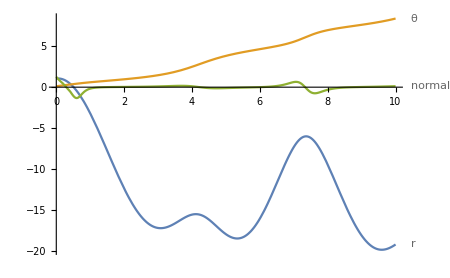

```mathematica
Plot[Evaluate@sol,{t,0,10},PlotLabels->{r,θ,normal}]
```

### Cleanup

```mathematica
With[{context="es`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Basic pendulum

```mathematica
With[{context="p1`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### Step 2: Parameters

```mathematica
params=<| m->1, g->9.8 ,l->2|>
```

<|m→1,g→9.8,l→2|>

### Step 3: Define forces

```mathematica
fg =m g RotationMatrix[θ[t]].(-rhat);
ftension=tension[t] rhat;
```

### Step 4: Equations of motion

```mathematica
(* Mass motion *)
eq1=fg+ftension==m polaraccel[];
eqns=splitVectorEqn[eq1]
```

{-g m Cos[θ[t]]+tension[t]==m (-r[t] θ'[t]^2+r''[t]),-g m Sin[θ[t]]==m (2 r'[t] θ'[t]+r[t] θ''[t])}

```mathematica
(* Constraints *)
```

```mathematica
constraint=r[t]==l;
```

### Step 5: Solve

```mathematica
sol=NDSolveValue[{eqns,constraint}/.params,{θ[t]},{t,0,10},Method->{"IndexReduction"->{"Pantelides", "ConstraintMethod"->"Projection"}}]
```

NDSolveValue::chknic: Structural analysis indicates that 2 initial conditions are needed to fix the state of the system. Currently only 0 initial conditions are specified. NDSolve may return one of a family of solutions.

{InterpolatingFunction[{{0., 10.}}, <>][t]}

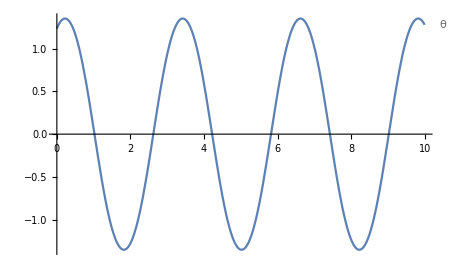

```mathematica
Plot[Evaluate@sol,{t,0,10},PlotLabels->{θ}]
```

### Cleanup

```mathematica
With[{context="p1`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Segway pendulum

```mathematica
With[{context="p2`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### Step 2: Parameters

```mathematica
params=<| m->1, g->9.8 ,l->2|>
```

<|m→1,g→9.8,l→2|>

### Step 3: Define forces

```mathematica
xhat=RotationMatrix[-θ[t]].(-θhat);
```

```mathematica
fg =m g RotationMatrix[θ[t]].(-rhat);
ftension=tension[t] rhat;
```

### Step 4: Equations of motion

```mathematica
(* Mass motion *)
eq1=fg+ftension==m( polaraccel[]+x''[t] xhat);
eqns=splitVectorEqn[eq1]
```

{-g m Cos[θ[t]]+tension[t]==m (-r[t] θ'[t]^2+r''[t]-Sin[θ[t]] x''[t]),-g m Sin[θ[t]]==m (2 r'[t] θ'[t]-Cos[θ[t]] x''[t]+r[t] θ''[t])}

```mathematica
(* Constraints *)
```

```mathematica
constraint=r[t]==l;
```

```mathematica
(* Driving functions *)
```

```mathematica
driver=x[t]==Sin[2 t];
```

### Step 5: Solve

```mathematica
sol=NDSolveValue[{eqns,constraint,driver}/.params,{θ[t],x[t]},{t,0,10},Method->{"IndexReduction"->{"Pantelides", "ConstraintMethod"->"Projection"}}]
```

NDSolveValue::chknic: Structural analysis indicates that 2 initial conditions are needed to fix the state of the system. Currently only 0 initial conditions are specified. NDSolve may return one of a family of solutions.

{InterpolatingFunction[{{0., 10.}}, <>][t],InterpolatingFunction[{{0., 10.}}, <>][t]}

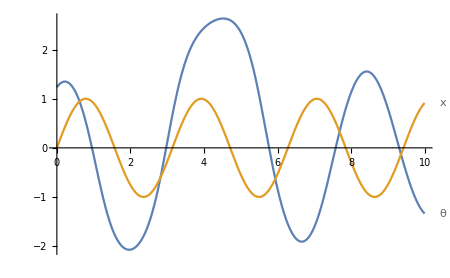

```mathematica
Plot[Evaluate@sol,{t,0,10},PlotLabels->{θ,x}]
```

### Cleanup

```mathematica
With[{context="p2`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Wheeled segway

```mathematica
With[{context="p3`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### Step 2: Parameters

```mathematica
params=<| m1->1,m2->2, g->9.8 ,l->2|>
```

<|m1→1,m2→2,g→9.8,l→2|>

### Step 3: Define forces

```mathematica
xhat=RotationMatrix[-θ[t]].(-θhat);
```

```mathematica
fg =m1 g RotationMatrix[θ[t]].(-rhat);
ftension=tension[t] rhat;
fdrive=drive[t] xhat;
```

### Step 4: Equations of motion

```mathematica
(* Mass motion *)
eq1=fg+ftension==m1 (polaraccel[]+x''[t] xhat);
(* Base motion *)
eq2=-ftension+fdrive==m2 x''[t] xhat;
eqns=Join[splitVectorEqn[eq1],splitVectorEqn[eq2]]
```

{-g m1 Cos[θ[t]]+tension[t]==m1 (-r[t] θ'[t]^2+r''[t]-Sin[θ[t]] x''[t]),-g m1 Sin[θ[t]]==m1 (2 r'[t] θ'[t]-Cos[θ[t]] x''[t]+r[t] θ''[t]),-drive[t] Sin[θ[t]]-tension[t]==-m2 Sin[θ[t]] x''[t],-Cos[θ[t]] drive[t]==-m2 Cos[θ[t]] x''[t]}

```mathematica
(* Constraints *)
```

```mathematica
constraint=r[t]==l;
```

```mathematica
(* Driving functions *)
```

```mathematica
driver={x[t]==0};
```

### Step 5: Solve

```mathematica
sol=NDSolveValue[{eqns,constraint,driver}/.params,{θ[t],x[t]},{t,0,10},Method->{"IndexReduction"->{"Pantelides", "ConstraintMethod"->"Projection"}}]
```

NDSolveValue::overdet: There are fewer dependent variables, {r[t],tension[t],x[t],θ[t]}, than equations, so the system is overdetermined.

NDSolveValue[{{-9.8 Cos[θ[t]]+tension[t]==-r[t] θ'[t]^2+r''[t]-Sin[θ[t]] x''[t],-9.8 Sin[θ[t]]==2 r'[t] θ'[t]-Cos[θ[t]] x''[t]+r[t] θ''[t],-tension[t]==-2 Sin[θ[t]] x''[t],0==-2 Cos[θ[t]] x''[t]},r[t]==2,{x[t]==0}},{θ[t],x[t]},{t,0,10},Method→{IndexReduction→{Pantelides,ConstraintMethod→Projection}}]

```mathematica
Plot[Evaluate@sol,{t,0,10},PlotLabels->{θ}]
```

NDSolveValue::dsvar: 0.000204286 cannot be used as a variable.

NDSolveValue::dsvar: 0.204286 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

-Graphics-

### Cleanup

```mathematica
With[{context="p3`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Scratch Work

```mathematica
exportNotebookPDF[]
```

/home/eric/Documents/School/QEA2/Module 3/Int 1/Mathematica work.pdf

```mathematica
Rotate[{0,1},Pi/3]
```

{0,1}

### Step 5: Constraints

```mathematica
constraint = r[t]==1
```

r[t]==1

```mathematica
Module[{r=r},
r[t_]:=l;
Simplify[eqns]
]
```

{g m Cos[θ]==motor[t]+l m θ'[t]^2,normal[t]==m (g Sin[θ]+l θ''[t])}